```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 2150 Kb

{Utilities`CleanSlate`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,Parallel`Debug`Perfmon`,Parallel`Debug`,System`,Global`}

```mathematica
Clear[rM]
rM = { x[t] , 0 }
```

{x[t],0}

```mathematica
D[rM, t]
```

{x'[t],0}

```mathematica
D[rM, t] . D[rM, t]
```

x'[t]^2

```mathematica
Clear[rm]
rm = { x[t] + b Sin[θ[t]] , - b Cos[θ[t]] }
```

{b Sin[θ[t]]+x[t],-b Cos[θ[t]]}

```mathematica
D[rm, t]
```

{x'[t]+b Cos[θ[t]] θ'[t],b Sin[θ[t]] θ'[t]}

```mathematica
D[rm, t] . D[rm, t]
```

b^2 Sin[θ[t]]^2 θ'[t]^2+(x'[t]+b Cos[θ[t]] θ'[t])^2

```mathematica
D[rm, t] . D[rm, t]  // Expand
```

x'[t]^2+2 b Cos[θ[t]] x'[t] θ'[t]+b^2 Cos[θ[t]]^2 θ'[t]^2+b^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
D[rm, t] . D[rm, t]  // Expand  // Simplify
```

x'[t]^2+2 b Cos[θ[t]] x'[t] θ'[t]+b^2 θ'[t]^2

```mathematica
Clear[T]
T = 1/2 M ( D[rM, t] . D[rM, t]  ) + 1/2 m ( D[rm, t] . D[rm, t]  // Expand  // Simplify )
```

1/2 M x'[t]^2+1/2 m (x'[t]^2+2 b Cos[θ[t]] x'[t] θ'[t]+b^2 θ'[t]^2)

```mathematica
Clear[V]
V =  - m g b Cos[θ[t]]
```

-b g m Cos[θ[t]]

```mathematica
Clear[ℒ]
ℒ = T - V
```

b g m Cos[θ[t]]+1/2 M x'[t]^2+1/2 m (x'[t]^2+2 b Cos[θ[t]] x'[t] θ'[t]+b^2 θ'[t]^2)

```mathematica
(* Put this down below for part b *)
```

```mathematica
Clear[ℒapproximate]
ℒapproximate = 
Normal[Series[ℒ , { θ[t] ,  0 , 2 } ]]  // Expand  // Factor
```

1/2 (2 b g m-b g m θ[t]^2+m x'[t]^2+M x'[t]^2+2 b m x'[t] θ'[t]-b m θ[t]^2 x'[t] θ'[t]+b^2 m θ'[t]^2)

```mathematica
Clear[q]
q = { x[t] , θ[t] }
```

{x[t],θ[t]}

```mathematica
EulerEquations[ ℒapproximate , q , t ]  // TableForm
```

b m θ[t] θ'[t]^2-(m+M) x''[t]-b m θ''[t]+1/2 b m θ[t]^2 θ''[t]==0
-1/2 b m (2 g θ[t]-θ[t]^2 x''[t]+2 (x''[t]+b θ''[t]))==0

```mathematica
D[ D[ ℒ , D[q[[1]], t] ] , t ] - D[ ℒ , q[[1]] ] 
D[ D[ ℒ , D[q[[2]], t] ] , t ] - D[ ℒ , q[[2]] ] // Expand // Simplify
```

M x''[t]+1/2 m (-2 b Sin[θ[t]] θ'[t]^2+2 x''[t]+2 b Cos[θ[t]] θ''[t])

b m (g Sin[θ[t]]+Cos[θ[t]] x''[t]+b θ''[t])

```mathematica
Table[
D[ D[ ℒ , D[q[[i]], t] ] , t ] - D[ ℒ , q[[i]] ], 
{ i,1, 2 } ] //Expand // Simplify //  TableForm
```

-b m Sin[θ[t]] θ'[t]^2+(m+M) x''[t]+b m Cos[θ[t]] θ''[t]
b m (g Sin[θ[t]]+Cos[θ[t]] x''[t]+b θ''[t])

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q, t ]  ;
eqs // TableForm
```

b m Sin[θ[t]] θ'[t]^2-(m+M) x''[t]-b m Cos[θ[t]] θ''[t]==0
-b m (g Sin[θ[t]]+Cos[θ[t]] x''[t]+b θ''[t])==0

```mathematica
Clear[parameters]
parameters = { 
M-> 40 , 
m-> 20 , 
g-> 9.8 , 
b -> 0.5 
} ;
parameters // TableForm
```

M→40
m→20
g→9.8
b→0.5

```mathematica
eqs /. parameters // TableForm
```

10. Sin[θ[t]] θ'[t]^2-60 x''[t]-10. Cos[θ[t]] θ''[t]==0
-10. (9.8 Sin[θ[t]]+Cos[θ[t]] x''[t]+0.5 θ''[t])==0

```mathematica
Clear[ics]
ics = { 
x[0] == 0 ,
x'[0] == 0 ,
θ[0] == π / 3 ,
θ'[0] == 0 
} ;
ics // TableForm
```

x[0]==0
x'[0]==0
θ[0]==π/3
θ'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[NDSolve[ Union[ eqs /. parameters, ics ] , q , { t, 0, 100 } ]]
```

{x[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q/. solution[t] ]  , { t, 0, 2 } , PlotLabels-> q  ]
```

-Graphics-

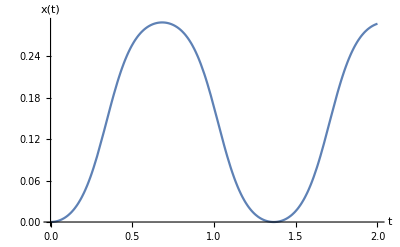

```mathematica
Plot[ q[[1]]/. solution[t] , { t, 0, 2 }  , AxesLabel-> { t , q[[1]] } ]
```

```mathematica
solution[t]
solution[t][[1]]
solution[t][[1,2]]
```

{x[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}

x[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

```mathematica
Animate[
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 0.1 , 10 } ]
```

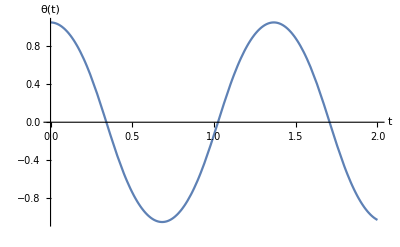

```mathematica
Plot[ q[[2]]/. solution[t] , { t, 0, 2 }, AxesLabel-> { t , q[[2]] }  ]
```

```mathematica
solution[t]
solution[t][[2]]
solution[t][[2,2]]
```

{x[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}

θ[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, tmax } , AxesLabel-> { q[[2]] , D[q[[2]], t] } ]  ,
{ tmax , 0.1 , 10 } ]
```

```mathematica
ℒ
D[ D[ ℒ , D[q[[1]], t] ] , t ] - D[ ℒ , q[[1]] ] 
D[ D[ ℒ , D[q[[2]], t] ] , t ] - D[ ℒ , q[[2]] ] // Expand // Simplify 
Normal[Series[ Cos[θ[t]] , { θ[t] , 0, 1} ] ]
Normal[Series[ Cos[θ[t]] , { θ[t] , 0, 2} ] ]
Normal[Series[ Sin[θ[t]] , { θ[t] , 0, 1 } ]  ]
```

b g m Cos[θ[t]]+1/2 M x'[t]^2+1/2 m (x'[t]^2+2 b Cos[θ[t]] x'[t] θ'[t]+b^2 θ'[t]^2)

M x''[t]+1/2 m (-2 b Sin[θ[t]] θ'[t]^2+2 x''[t]+2 b Cos[θ[t]] θ''[t])

b m (g Sin[θ[t]]+Cos[θ[t]] x''[t]+b θ''[t])

1

1-θ[t]^2/2

θ[t]